```mathematica
ClearAll["Global`*"];
Remove["Global`*"];

CalculateSMatrix2[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_,nGrid_]:= Module[{y,x,L,RHS,RHS2,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t,sTable,s,time1,dT,time2},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState]; (* Fix this *)
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
RHS[i_] :=(IdentityMatrix[4] + Afᵀ.Subscript[s, i] + Subscript[s, i].Af - KroneckerProduct[Subscript[s, i].Bf,Bfᵀ.Subscript[s, i]]) /. {x-> x1a[τ - i*τ/nGrid], xdot -> xdot1a[τ - i*τ/nGrid], θ ->θ1a[τ - i*τ/nGrid], θdot -> θdot1a[τ - i*τ/nGrid], u -> u1a[τ - i*τ/nGrid]}; 
Subscript[s, 0] = S0;
dT = τ/nGrid;
sTable = Table[Subscript[s, i+1] = Subscript[s, i] + dT*RHS[i],{i,0,nGrid}];
sTable
]
CalculateSMatrix[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_]:=Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},xState={x,xdot,θ,θdot};x2dot=(u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ])/(1-A Cos[θ]^2);θ2dot=(-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]))/(1-A Cos[θ]^2);fx={xdot,x2dot,θdot,θ2dot};L=u^2/2;Af=fxxState;Bf=D[fx, u];Q=LxStatexState;Mf=D[L, u]xState;R=D[L, {u,2}];S0={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};RHS[t_]:=IdentityMatrix[4]+Transpose[Af].S[t]+S[t].Af-KroneckerProduct[S[t].Bf,Transpose[Bf].S[t]]/.{x->x1a[τ-t],xdot->xdot1a[τ-t],θ->θ1a[τ-t],θdot->θdot1a[τ-t],u->u1a[τ-t]};sol2=S/.NDSolve[{S'[t]==RHS[t],S[0]==S0},S,{t,0,τ}];S=sol2⟦1⟧]
CalculateGains2[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,sTable_,nGrid_]:= Module[{index,x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
index = Round[τ - time,τ/nGrid]/(τ/nGrid);
K = (Bfᵀ.Indexed[sTable,1+index])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]
CalculateGains[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,S_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
K = (Bfᵀ.S[τ - time])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]

ffCartPendulum[ICs_,n_?NumericQ,τ_?NumericQ,τ1_?NumericQ,A_?NumericQ,order_?NumericQ,maxIter_?NumericQ,maxError_?NumericQ,uMax_?NumericQ,maxCount_?NumericQ,initGuess_,maxJ_?NumericQ]:=
Module[{frootNew,errorNew,InitGuess,J,S,K,count,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};

InitGuess = initGuess;
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];

bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];

sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

froot=FindRoot[eqns,sv,MaxIterations->maxIter];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];

count = 0;

(*Print["Error First Guess = ",error];*)

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
While[((error > maxError) || (J > maxJ)) && count <= maxCount ,
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

frootNew=FindRoot[eqns,sv,MaxIterations->maxIter];
errorNew = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.frootNew,"Frobenius"];
If[errorNew <= error,froot = frootNew;error = errorNew;
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
,_];
count = count+1;

(*Print["Count Shooting= ",count,"    Error New = ",errorNew,"    Error Min = ",error];*)

];


xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
S = CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A];
K[time_] := CalculateGains[xff,xdotff,θff,θdotff,uff,time,A,τ,S];
{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}]
ffCartPendulum2[ICs_,n_,τ_,τ1_,A_,order_,maxIter_,maxError_,uMax_,maxCount_,initGuess_,maxJ_,nGrid_]:=
Module[{time1,time2,sTable,frootNew,errorNew,InitGuess,J,S,K,count,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,
θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess=Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
xdot,(A θdot^2 Sin[θ]+(λ4 Cos[θ]-λ2)/(1-A Cos[θ]^2)+A Cos[θ] Sin[θ])/(1-A Cos[θ]^2),θdot,(-(-λ2 Cos[θ]+λ4 Cos[θ]^2)/(1-A Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ])/(1-A Cos[θ]^2),
0,-λ1,1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
(4 (A θdot Sin[θ] (λ2-λ4 Cos[θ])))/(A Cos[2 θ]+A-2)-λ3};
InitGuess=initGuess;
xGuess=Table[If[i≠-1,Subscript[xGuess, i+1]=Subscript[xGuess, i]+Δt f[Subscript[xGuess, i]],
Subscript[xGuess, 0]={ICs⟦1⟧,ICs⟦2⟧,ICs⟦3⟧,ICs⟦4⟧,InitGuess⟦1⟧,InitGuess⟦2⟧,InitGuess⟦3⟧,InitGuess⟦4⟧}],{i,-1,n-1}];
bcs={Subscript[x, 0]==ICs⟦1⟧,Subscript[xdot, 0]==ICs⟦2⟧,Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs⟦3⟧,Subscript[θdot, 0]==ICs⟦4⟧,Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[x, i],xGuess⟦i+1⟧⟦1⟧},{Subscript[xdot, i],xGuess⟦i+1⟧⟦2⟧},{Subscript[θ, i],xGuess⟦i+1⟧⟦3⟧},{Subscript[θdot, i],xGuess⟦i+1⟧⟦4⟧},{Subscript[λ1, i],xGuess⟦i+1⟧⟦5⟧},{Subscript[λ2, i],xGuess⟦i+1⟧⟦6⟧},{Subscript[λ3, i],xGuess⟦i+1⟧⟦7⟧},{Subscript[λ4, i],xGuess⟦i+1⟧⟦8⟧}},{i,0,n}],1];
{time1,froot}=Timing[FindRoot[eqns,sv,MaxIterations->maxIter]];
error=Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]}-{0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]}-ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];
count=0;uff0=ListInterpolation[Table[(Subscript[λ4, i] Cos[Subscript[θ, i]]-Subscript[λ2, i])/(1-A Cos[Subscript[θ, i]]^2),{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
J=NIntegrate[uff0[t]^2,{t,0,τ}];
While[(error>maxError||J>maxJ)&&count≤maxCount,
InitGuess={RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess=Table[If[i≠-1,Subscript[xGuess, i+1]=Subscript[xGuess, i]+Δt f[Subscript[xGuess, i]],Subscript[xGuess, 0]={ICs⟦1⟧,ICs⟦2⟧,ICs⟦3⟧,ICs⟦4⟧,InitGuess⟦1⟧,InitGuess⟦2⟧,InitGuess⟦3⟧,InitGuess⟦4⟧}],{i,-1,n-1}];
sv=Flatten[Table[{{Subscript[x, i],xGuess⟦i+1⟧⟦1⟧},{Subscript[xdot, i],xGuess⟦i+1⟧⟦2⟧},{Subscript[θ, i],xGuess⟦i+1⟧⟦3⟧},{Subscript[θdot, i],xGuess⟦i+1⟧⟦4⟧},{Subscript[λ1, i],xGuess⟦i+1⟧⟦5⟧},{Subscript[λ2, i],xGuess⟦i+1⟧⟦6⟧},{Subscript[λ3, i],xGuess⟦i+1⟧⟦7⟧},{Subscript[λ4, i],xGuess⟦i+1⟧⟦8⟧}},{i,0,n}],1];
frootNew=FindRoot[eqns,sv,MaxIterations->maxIter];
errorNew=Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]}-{0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]}-ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.frootNew,"Frobenius"];
If[errorNew≤error,froot=frootNew;error=errorNew;uff0=ListInterpolation[Table[(Subscript[λ4, i] Cos[Subscript[θ, i]]-Subscript[λ2, i])/(1-A Cos[Subscript[θ, i]]^2),{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
J=NIntegrate[uff0[t]^2,{t,0,τ}];,_];
count=count+1;
(*Print["Count Shooting= ",count,"    Error New = ",errorNew,"    Error Min = ",error];*)
];
xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
λ1ff0=ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
λ2ff0=ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
λ3ff0=ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
λ4ff0=ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
uff0=ListInterpolation[Table[(Subscript[λ4, i] Cos[Subscript[θ, i]]-Subscript[λ2, i])/(1-A Cos[Subscript[θ, i]]^2),{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
J=NIntegrate[uff0[t]^2,{t,0,τ}];
sTable=CalculateSMatrix2[xff,xdotff,θff,θdotff,uff,τ,A,nGrid];
K[time_]:=CalculateGains2[xff,xdotff,θff,θdotff,uff,time,A,τ,sTable,nGrid];{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}]

testSwingUp[ICs_,τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t,J},eq={x'[t]==xdot[t],xdot'[t]==(uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]])/(1-A Cos[θ[t]]^2),θ'[t]==θdot[t],θdot'[t]==(-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))/(1-A Cos[θ[t]]^2)};init={x[0]==ICs⟦1⟧,xdot[0]==ICs⟦2⟧,θ[0]==ICs⟦3⟧,θdot[0]==ICs⟦4⟧};{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];J=NIntegrate[uff0[t]^2,{t,0,τ}];{xs,xdots,θs,θdots,uff0,J}]

testWithFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},κ1=κ2=3;κ3=-0.1;κ4=-0.65;xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];ufb[t_]:=Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0≤t≤τ}},κ1 (θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3 (xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];u[t_]:=uff[t]+ufb[t];eq={x'[t]==xdot[t],xdot'[t]==(u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]])/(1-A Cos[θ[t]]^2),θ'[t]==θdot[t],θdot'[t]==(-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))/(1-A Cos[θ[t]]^2)};init={x[0]==ICs⟦1⟧,xdot[0]==ICs⟦2⟧,θ[0]==ICs⟦3⟧,θdot[0]==ICs⟦4⟧};{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];us[t_]:=uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0≤t≤τ}},κ1 (θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3 (xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];J=NIntegrate[us[t]^2,{t,0,τ}];{xs,xdots,θs,θdots,us,J}]

testWithFBClipped[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,uBound_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},κ1=κ2=3;κ3=-0.1;κ4=-0.65;xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];ufb[t_]:=Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0≤t≤τ}},κ1 (θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3 (xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];u[t_]:=Clip[uff[t]+ufb[t],{-uBound,uBound}];eq={x'[t]==xdot[t],xdot'[t]==(u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]])/(1-A Cos[θ[t]]^2),θ'[t]==θdot[t],θdot'[t]==(-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))/(1-A Cos[θ[t]]^2)};init={x[0]==ICs⟦1⟧,xdot[0]==ICs⟦2⟧,θ[0]==ICs⟦3⟧,θdot[0]==ICs⟦4⟧};{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];us[t_]:=Clip[uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0≤t≤τ}},κ1 (θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3 (xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])],{-uBound,uBound}];J=NIntegrate[us[t]^2,{t,0,τ}];{xs,xdots,θs,θdots,us,J}]

Energy[{x1_,x2_,θ1_,θ2_,A_}] := 1/2*x2^2 + 1/2*A*θ2^2 + A*Cos[θ1]*x2*θ2 - A*Cos[θ1];
```

Remove::rmnsm: There are no symbols matching "Global`*".

Initial Conditions = {0,0.808789,-0.379552,0.333731}

Energy = 0.202582

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 30 iterations.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$176140 near {t$176140} = {1.04484}. NIntegrate obtained 2.42884 and 0.00437348 for the integral and error estimates.

Count = 1

Error = 2.14646

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 30 iterations.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$176463 near {t$176463} = {0.712813}. NIntegrate obtained 0.801178 and 0.00342637 for the integral and error estimates.

Count = 2

Error = 0.847736

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$176662 near {t$176662} = {4.87074193870817}. NIntegrate obtained 0.450087 and 0.0000599415 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Count = 3

Error = 0.337045

Total Time for Convergence = 5

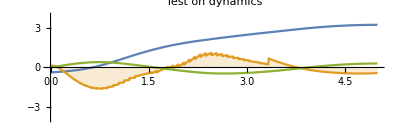
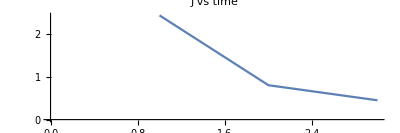
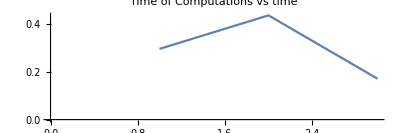
-Graphics- | -Graphics- | -Graphics-

```mathematica
n = 10; τ = 5; τ1 = τ*1.25 ;order = 5;maxIter = 30;uBound = 5;maxCount = 10;maxJ = 2^2*τ;nGrid = 60;
M =3; (*M is the no of times the solution will be recomputed in time τ  *)
A = 0.2;maxError = 0.01;
maxErrorInitial = 0.5;
MyAppend[f1_, f2_, T1_, dT_] := Module[{f},
    f[t_] := Piecewise[{{f1[t], 0 <= t <= T1}, {f2[t - T1], T1 <= t <= T1 + dT}}];
    f];
EInitial = 2;
While[EInitial > 1.5 || EInitial < 0.5,
xdotMin = -1;
xdotMax = 1;
θMin = -π;
θMax = π;
θdotMin = -1;
θdotMax = 1;
xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit};
EInitial = Energy[Join[Table[ICs[[i]],{i,1,4}],{A}]];
];
ICs = ICData[[5]];
Print["Initial Conditions = ",ICs];
EInitial = Energy[Join[Table[ICs[[i]],{i,1,4}],{A}]];
Print["Energy = ", EInitial];
xf[t_] := 0;
xdotf[t_] := 0;
θf[t_] := 0;
θdotf[t_] := 0;
Js = {};
timeData = {};
errorInitial = 10;
initGuess = {0,0,0,0};
count = 0;
Tmax = 20;
maxcountAlgo = Tmax*M/τ;
InitGuess = {0,0,0,0};
While[errorInitial > maxErrorInitial && count < maxcountAlgo,
{time,{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}}=Timing[ffCartPendulum2[ICs,n,τ,τ1,A,order,maxIter,maxError,uBound,maxCount,InitGuess,maxJ,nGrid]]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J}=testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uBound,K];
ICs = {x1b[τ*1/M], xdot1b[τ*1/M], θ1b[τ*1/M], θdot1b[τ*1/M]};
errorInitial = Norm[ICs - {0,0,π,0}];
initGuess = {λ1ff0[τ*1/M],λ2ff0[τ*1/M],λ3ff0[τ*1/M],λ4ff0[τ*1/M]};
xf = MyAppend[xf, x1b, τ*count/M, τ*1/M];
xdotf = MyAppend[xdotf, xdot1b, τ*count/M, τ*1/M];
  θf = MyAppend[θf, θ1b, τ*count/M, τ*1/M];
θdotf = MyAppend[θdotf, θdot1b, τ*count/M, τ*1/M];
uf = MyAppend[uf, u1b, τ*count/M, τ*1/M];
Js = Append[Js,J];
count = count + 1;	
timeData = Append[timeData,time];
Print["Count = ",count];
Print["Error = ",errorInitial];	
]
p1a = Plot[{θf[t], uf[t], xf[t]}, {t, 0, τ*1/M*count}, PlotRange -> {-4, 4}, Filling -> {2 -> Axis}, PlotLegends -> {"θ1b", "u1b", "x1b"}, PlotLabel -> "Test on dynamics", AspectRatio -> 1/3, ImageSize -> 400, GridLines -> {None, {-π, π}}];
p1b = ListLinePlot[Js,AspectRatio -> 1/3, ImageSize -> 400,PlotLabel->"J vs time"];
p1c = ListLinePlot[timeData,AspectRatio -> 1/3, ImageSize -> 400,PlotLabel->"Time of Computations vs time"];
Print["Total Time for Convergence = ",τ*1/M*count];
Grid[{{p1a,p1b,p1c}}]
```

### Script for collecting Testing Data

```mathematica
ICData = Import["ICDataComputation20.mx"];
EData = Import["EDataComputation20.mx"];
MyAppend[f1_, f2_, T1_, dT_] := Module[{f},
    f[t_] := Piecewise[{{f1[t], 0 <= t <= T1}, {f2[t - T1], T1 <= t <= T1 + dT}}];
    f]; 
MPCVariant[A1_,A2_,n_,M_,uBound_,ICs_,nGrid_] := Module[{totalTime,τ,τ1,order,maxCount,maxJ,maxError,maxErrorInitial,EInitial,xdotMin,xdotMax,
θMin,Tmax,θMax,θdotMin,θdotMax,xdotInit,θInit,θdotInit,maxIter,errorInitial,initGuess,count,maxcountAlgo,x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K,
x1b,xdot1b,θ1b,θdot1b,u1b,ICinit,time,timeData,InitGuess},
 τ = 5; τ1 = τ*1.25 ;order = 5;maxIter = 30;maxCount = 10;maxJ = 2^2*τ;
maxError = 0.01;
maxErrorInitial = 0.5;
ICinit = ICs;
EInitial = Energy[Join[Table[ICs[[i]],{i,1,4}],{A2}]];
errorInitial = 10;
InitGuess = {0,0,0,0};
count = 0;
Tmax = 20;
maxcountAlgo = Tmax*M/τ;
timeData = {};
While[errorInitial > maxErrorInitial && count < maxcountAlgo,
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}=Quiet[ffCartPendulum2[ICinit,n,τ,τ1,A1,order,maxIter,maxError,uBound,maxCount,InitGuess,maxJ,nGrid]]; {x1b,xdot1b,θ1b,θdot1b,u1b,J}=Quiet[testWithFBClipped[ICinit,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A2,uBound,K]];ICinit = {x1b[τ*1/M], xdot1b[τ*1/M], θ1b[τ*1/M], θdot1b[τ*1/M]};

errorInitial = Norm[ICinit - {0,0,π,0}];
InitGuess = {λ1ff0[τ*1/M],λ2ff0[τ*1/M],λ3ff0[τ*1/M],λ4ff0[τ*1/M]};
count = count + 1;	
];
totalTime = τ*1/M*count]
```

### Collect Data for all ICData with m varying

```mathematica
ICData = Import["ICDataComputation20.mx"];
EData = Import["EDataComputation20.mx"];
numberTests = 50;
n = 20;M = 10;uBound = 5;nGrid = 60;
A1 = 0.2;A2 = 0.2;

SetSharedVariable[TimingDataConv];
SetSharedVariable[MedianData];
ParallelTable[
Block[{timeConvergence,ICs},
ICs = ICData[[iter]];
timeConvergence =MPCVariant[A1,A2,n,M,uBound,ICs,nGrid];
AppendTo[TimingDataConv,timeConvergence];
Export["TimingDataConv10.mx",TimingDataConv];
];
,
{iter,45,numberTests}
];
```

```mathematica
TimingDataConv3 = Import["TimingDataConv3.mx"];
TimingDataConv5 = Import["TimingDataConv5.mx"];
TimingDataConv10 = Import["TimingDataConv10.mx"];
```

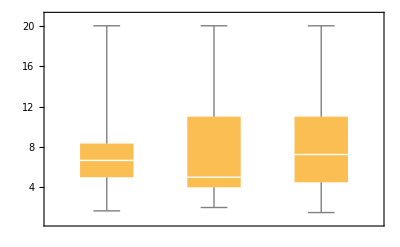

```mathematica
BoxWhiskerChart[{TimingDataConv3,TimingDataConv5,TimingDataConv10}]
```

## Conduct Simulations with varying n and M = 3

```mathematica
ICData = Import["ICDataComputation20.mx"];
EData = Import["EDataComputation20.mx"];
numberTests = 200;
n = 10;M = 3;uBound = 5;nGrid = 60;
A1 = 0.2;A2 = 0.2;
TimingDataConv = {};
SetSharedVariable[TimingDataConv];
ParallelTable[
Block[{timeConvergence,ICs},
ICs = ICData[[iter]];
timeConvergence =MPCVariant[A1,A2,n,M,uBound,ICs,nGrid];
AppendTo[TimingDataConv,timeConvergence];
Print["Iter = ",iter,"   Time of Convergence = ",timeConvergence];
Export["TimingDataConvN10.mx",TimingDataConv];
];
,
{iter,1,numberTests}
];
```

Iter = 168   Time of Convergence = 20/3

Iter = 173   Time of Convergence = 35/3

Iter = 177   Time of Convergence = 15

Iter = 178   Time of Convergence = 5

Iter = 174   Time of Convergence = 20

Iter = 175   Time of Convergence = 20/3

Iter = 181   Time of Convergence = 20

Iter = 169   Time of Convergence = 20

Iter = 176   Time of Convergence = 20/3

Iter = 179   Time of Convergence = 20

Iter = 182   Time of Convergence = 5

Iter = 170   Time of Convergence = 20/3

Iter = 180   Time of Convergence = 5

Iter = 189   Time of Convergence = 25/3

Iter = 185   Time of Convergence = 20

Iter = 190   Time of Convergence = 5

Iter = 183   Time of Convergence = 55/3

Iter = 171   Time of Convergence = 20

Iter = 191   Time of Convergence = 20/3

Iter = 172   Time of Convergence = 20/3

Iter = 184   Time of Convergence = 20/3

Iter = 193   Time of Convergence = 20/3

Iter = 186   Time of Convergence = 50/3

Iter = 194   Time of Convergence = 20/3

Iter = 197   Time of Convergence = 20

Iter = 195   Time of Convergence = 25/3

Iter = 198   Time of Convergence = 5

Iter = 196   Time of Convergence = 25/3

Iter = 187   Time of Convergence = 20

Iter = 188   Time of Convergence = 20

Iter = 199   Time of Convergence = 20

Iter = 200   Time of Convergence = 20

$Aborted

```mathematica
Export["TimingDataConvN10.mx",TimingDataConv];
```

```mathematica
TimingDataConv = {5,20/3,50/3,5,20,20/3,40/3,10/3,5,5,25/3,20,20,15,20,20/3,20,20,5,20/3,5/3,5,10/3,20,20/3,20/3,20/3,20,20,5,20,5,55/3,20/3,20,20,20/3,20,50/3,20/3,5/3,35/3,10,20,20/3,10/3,20,20/3,10/3,35/3,20,20/3,20/3,20,5,15,20/3,55/3,20,5,20/3,20/3,25/3,5,5/3,20,20,40/3,40/3,20,20,5,10/3,20/3,20,20,5,20,20,20,20,20,20,20,25/3,10,20/3,25/3,20/3,35/3,20/3,25/3,20,20/3,20,25/3,20,5,15,20,20,20/3,20,20,20,20/3,20,20/3,20,20,10,20,10,20,20/3,20,25/3,20,20,20,20,20/3,20,20,20/3,20,20,20,20/3,20/3,20,20,25/3,20,15,20/3,20/3,20,25/3,40/3,15,20,10,20,5,25/3,20/3,5,10,55/3,55/3,20,20/3,20/3,5,20,20,25/3,35/3,20/3,20,10,15,20/3,5,20/3,5,20/3,35/3,15,5,20,20/3,20,20,20/3,20,5,20/3,5,25/3,20,5,55/3,20,20/3,20/3,20/3,20/3,50/3,20/3,20,25/3,5,25/3,20,20,20,20,40/3}
```

{5,20/3,50/3,5,20,20/3,40/3,10/3,5,5,25/3,20,20,15,20,20/3,20,20,5,20/3,5/3,5,10/3,20,20/3,20/3,20/3,20,20,5,20,5,55/3,20/3,20,20,20/3,20,50/3,20/3,5/3,35/3,10,20,20/3,10/3,20,20/3,10/3,35/3,20,20/3,20/3,20,5,15,20/3,55/3,20,5,20/3,20/3,25/3,5,5/3,20,20,40/3,40/3,20,20,5,10/3,20/3,20,20,5,20,20,20,20,20,20,20,25/3,10,20/3,25/3,20/3,35/3,20/3,25/3,20,20/3,20,25/3,20,5,15,20,20,20/3,20,20,20,20/3,20,20/3,20,20,10,20,10,20,20/3,20,25/3,20,20,20,20,20/3,20,20,20/3,20,20,20,20/3,20/3,20,20,25/3,20,15,20/3,20/3,20,25/3,40/3,15,20,10,20,5,25/3,20/3,5,10,55/3,55/3,20,20/3,20/3,5,20,20,25/3,35/3,20/3,20,10,15,20/3,5,20/3,5,20/3,35/3,15,5,20,20/3,20,20,20/3,20,5,20/3,5,25/3,20,5,55/3,20,20/3,20/3,20/3,20/3,50/3,20/3,20,25/3,5,25/3,20,20,20,20,40/3}

```mathematica
TimingDataConvN10 = Import["TimingDataConvN10.mx"]
TimingDataConvN20 = Import["TimingDataConvN20.mx"]
TimingDataConvN30 = Import["TimingDataConvN30.mx"]
TimingDataConvN50 = Import["TimingDataConvN50.mx"]
TimingDataConvN80 = Import["TimingDataConvN80.mx"]
```

{5,20/3,50/3,5,20,20/3,40/3,10/3,5,5,25/3,20,20,15,20,20/3,20,20,5,20/3,5/3,5,10/3,20,20/3,20/3,20/3,20,20,5,20,5,55/3,20/3,20,20,20/3,20,50/3,20/3,5/3,35/3,10,20,20/3,10/3,20,20/3,10/3,35/3,20,20/3,20/3,20,5,15,20/3,55/3,20,5,20/3,20/3,25/3,5,5/3,20,20,40/3,40/3,20,20,5,10/3,20/3,20,20,5,20,20,20,20,20,20,20,25/3,10,20/3,25/3,20/3,35/3,20/3,25/3,20,20/3,20,25/3,20,5,15,20,20,20/3,20,20,20,20/3,20,20/3,20,20,10,20,10,20,20/3,20,25/3,20,20,20,20,20/3,20,20,20/3,20,20,20,20/3,20/3,20,20,25/3,20,15,20/3,20/3,20,25/3,40/3,15,20,10,20,5,25/3,20/3,5,10,55/3,55/3,20,20/3,20/3,5,20,20,25/3,35/3,20/3,20,10,15,20/3,5,20/3,5,20/3,35/3,15,5,20,20/3,20,20,20/3,20,5,20/3,5,25/3,20,5,55/3,20,20/3,20/3,20/3,20/3,50/3,20/3,20,25/3,5,25/3,20,20,20,20,40/3}

{5,5,5,35/3,5,5,20/3,20/3,25/3,20/3,10/3,20/3,20/3,5,5,10/3,10,5/3,20/3,10/3,5,20/3,10,20,20/3,20,5,25/3,5,40/3,20/3,10/3,20/3,5,5,15,5,5/3,20,20/3,10/3,5,20,5,20/3,20,5/3,10/3,5,35/3,40/3,5,9/2,4,11,4,7,6,3,10,19/2,13/2,29/2,18,25/2,5,2,9,3/2,20,6,13/2,11,37/2,13/2,8,20,3,17/2,20,8,9/2,9/2,15/2,31/2,4,11/2,11,20,19/2,33/2,13/2,7/2,20,4,7/2,19/2,13/2,37/2,3/2,21/2,10/3,20/3,15,20,20,20,50/3,20/3,20,10/3,20/3,25/3,20/3,50/3,35/3,5/3,20/3,20/3,25/3,20/3,20/3,20/3,20,20/3,10/3,5,10/3,10/3,15,20/3,20/3,20,10/3,5,25/3,20/3,20/3,5,10/3,10/3,40/3,20,20/3,20/3,20/3,5,5/3,20/3,25/3,20,20/3,20,15,20/3,20/3,20,20,20,20/3,20,35/3,10/3,10,50/3,20/3,20/3,20/3,20/3,20/3,20,35/3,25/3,20,15,35/3,20,5,55/3,20,20/3,5,20/3,20/3,20,25/3,40/3,10,50/3,10/3,20,20/3,20/3,5,5,10,20/3,25/3,20,5}

{5,10/3,20/3,5,5/3,25/3,5,20,20/3,5,5,10/3,5,20/3,5,20/3,20/3,20/3,5,20,20/3,5,5/3,20/3,50/3,20/3,20,5,10,35/3,5,10/3,20/3,5,15,20/3,20/3,10/3,20/3,20/3,10/3,5,20/3,5,5,20/3,35/3,10,25/3,5,20/3,20,20/3,20/3,5,5,10,20/3,5,20/3,5,25/3,25/3,5,20/3,20/3,25/3,25/3,20/3,20,20/3,10,20/3,5,20,20/3,20/3,10/3,25/3,50/3,25/3,20/3,5/3,25/3,20/3,20/3,5,25/3,10,20/3,20/3,5,40/3,5,20/3,20,35/3,20/3,20/3,25/3,25/3,20/3,20,20/3,40/3,20/3,20/3,20/3,5,20,20/3,20,5,25/3,20,20/3,20/3,50/3,10/3,10/3,10/3,5,25/3,10/3,25/3,20/3,20/3,20/3,20,10/3,5,35/3,20/3,25/3,20/3,20/3,20/3,50/3,40/3,10/3,20,35/3,20/3,35/3,20/3,20/3,20/3,20/3,20/3,10,10/3,10/3,5,20/3,20,20,5/3,40/3,5,20/3,20/3,5,20/3,20/3,20/3,20/3,5,20,5,20,40/3,20,25/3,20/3,10/3,20/3,20/3,20/3,20/3,20/3,25/3,25/3,20/3,20,20/3,20/3,20/3,20/3,20/3,20,5,20/3,5,5,20/3,5,20/3,35/3,35/3,20/3}

{5,20/3,25/3,5,10,20/3,20/3,20/3,20/3,20/3,5,5/3,20/3,20/3,5,10/3,5,20/3,20/3,20/3,5,5,5,10,25/3,5,10,5,20/3,10/3,5,10,20/3,5,25/3,5,5/3,20/3,20/3,10/3,15,5,20/3,10/3,5,35/3,5,10/3,20/3,20/3,20/3,20/3,20/3,35/3,35/3,25/3,5,10,10,5,10,5,20/3,20/3,5,5/3,20/3,25/3,20/3,35/3,20/3,5,20/3,20/3,25/3,20/3,20/3,5,20/3,20/3,35/3,20/3,5,10,5,40/3,5,5,10/3,25/3,20/3,20/3,20/3,20/3,20/3,25/3,10,20/3,5,35/3,5,20/3,10/3,25/3,20/3,20/3,20/3,10/3,20,5,20,5,10/3,20/3,25/3,20/3,20/3,5,5,20/3,10,20/3,5,20/3,5,20/3,5,10/3,5,20/3,10/3,10/3,20/3,10/3,5,25/3,20/3,40/3,5,25/3,25/3,50/3,20/3,20/3,20/3,20/3,50/3,20/3,25/3,20/3,35/3,35/3,20/3,20/3,20/3,25/3,10,25/3,10/3,20/3,25/3,10,25/3,5,15,20/3,20/3,20/3,20/3,55/3,5,20/3,25/3,10/3,10,5,10,20/3,20/3,5,20/3,20/3,5,20/3,5,15,40/3,20/3,20/3,20/3,20/3,5,5,20/3,35/3,20/3,20/3,20/3,20/3,5}

{5,10/3,20/3,25/3,5,5/3,20/3,5,40/3,10/3,5,5,20/3,10/3,20/3,5,10,20/3,5,55/3,5,15,20/3,20/3,10/3,20,5,5,5/3,20/3,5,5,20/3,10/3,5,5,20/3,10/3,20/3,20,50/3,20,10,20/3,20/3,20/3,20,20/3,20/3,25/3,5,20,5,10/3,20/3,20/3,25/3,5,20/3,10,25/3,20,5,20/3,5,20/3,10,20/3,5/3,20/3,25/3,55/3,20,20/3,20/3,25/3,20,25/3,55/3,20/3,5,5,20,20/3,5,40/3,20,20/3,20,20/3,25/3,5,35/3,20/3,40/3,25/3,20/3,35/3,20/3,20,20/3,25/3,35/3,10,50/3,20/3,20/3,10/3,20/3,5,5,10,25/3,20/3,20/3,5,10/3,5,20/3,20/3,10/3,5,20,20,5,20/3,20/3,5,35/3,20/3,25/3,10/3,20/3,20/3,10/3,5,5,10/3,10/3,25/3,20,15,25/3,20/3,20/3,20/3,25/3,20/3,55/3,20/3,20/3,10,10,10/3,10/3,25/3,20/3,5,55/3,25/3,10/3,25/3,20/3,20,5,25/3,20/3,5,20/3,20/3,20/3,20/3,20/3,5,5,5/3,20/3,15,35/3,20/3,10/3,20/3,20/3,20/3,40/3,20,20/3,20/3,20/3,40/3,35/3,5,25/3,5,25/3,25/3,5,25/3,20/3,20/3}

```mathematica
TimingDataConv = {}
```

{}

```mathematica
Dimensions[TimingDataConv]
```

{200}

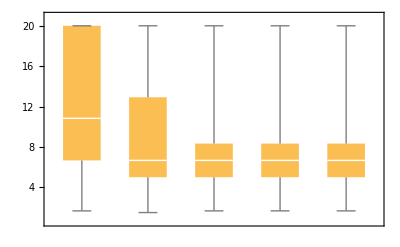

```mathematica
BoxWhiskerChart[{TimingDataConvN10,TimingDataConvN20,TimingDataConvN30,TimingDataConvN50,TimingDataConvN80}]
```